```mathematica
$PlotTheme="Scientific"
```

Scientific

```mathematica
SetOptions[{Plot,ListPlot,ArrayPlot,ContourPlot,DiscretePlot3D},BaseStyle->{14,Directive[FontFamily->"cmr10"]}];
```

# All intertwiners Immirzi 0.1

## Load the Data

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pdona/Dropbox/Ongoing Projects/OtherEPRLDivergences/Spinfoam_radiative_corrections/Notebooks

```mathematica
DATA = "../data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_0/self_energy_pcutoff_0.0.csv";
```

```mathematica
getfile[Dl_,K_]:=  StringJoin["../data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_",ToString[Dl],"/self_energy_pcutoff_",ToString[NumberForm[N[K],{3,1}]],".csv"];
```

```mathematica
getfile[0,1/2]
```

../data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_0/self_energy_pcutoff_0.5.csv

```mathematica
NumberForm[N[2],{3,1}]
```

2.0

```mathematica
A00KDl0 = {};
A01KDl0 = {};
A11KDl0 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[0,k],"Data",HeaderLines->1];
AppendTo[A00KDl0,{k,tmp00}];
AppendTo[A01KDl0,{k,tmp01}];
AppendTo[A11KDl0,{k,tmp11}];
]
```

```mathematica
A00KDl1 = {};
A01KDl1 = {};
A11KDl1 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[1,k],"Data",HeaderLines->1];
AppendTo[A00KDl1,{k,tmp00}];
AppendTo[A01KDl1,{k,tmp01}];
AppendTo[A11KDl1,{k,tmp11}];
]
```

```mathematica
A00KDl2 = {};
A01KDl2 = {};
A11KDl2 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[2,k],"Data",HeaderLines->1];
AppendTo[A00KDl2,{k,tmp00}];
AppendTo[A01KDl2,{k,tmp01}];
AppendTo[A11KDl2,{k,tmp11}];
]
```

```mathematica
A00KDl3 = {};
A01KDl3 = {};
A11KDl3 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[3,k],"Data",HeaderLines->1];
AppendTo[A00KDl3,{k,tmp00}];
AppendTo[A01KDl3,{k,tmp01}];
AppendTo[A11KDl3,{k,tmp11}];
]
```

```mathematica
A00KDl4 = {};
A01KDl4 = {};
A11KDl4 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[4,k],"Data",HeaderLines->1];
AppendTo[A00KDl4,{k,tmp00}];
AppendTo[A01KDl4,{k,tmp01}];
AppendTo[A11KDl4,{k,tmp11}];
]
```

```mathematica
A00KDl5 = {};
A01KDl5 = {};
A11KDl5 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[5,k],"Data",HeaderLines->1];
AppendTo[A00KDl5,{k,tmp00}];
AppendTo[A01KDl5,{k,tmp01}];
AppendTo[A11KDl5,{k,tmp11}];
]
```

```mathematica
A00KDl6 = {};
A01KDl6 = {};
A11KDl6 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[6,k],"Data",HeaderLines->1];
AppendTo[A00KDl6,{k,tmp00}];
AppendTo[A01KDl6,{k,tmp01}];
AppendTo[A11KDl6,{k,tmp11}];
]
```

```mathematica
A00KDl7 = {};
A01KDl7 = {};
A11KDl7 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[7,k],"Data",HeaderLines->1];
AppendTo[A00KDl7,{k,tmp00}];
AppendTo[A01KDl7,{k,tmp01}];
AppendTo[A11KDl7,{k,tmp11}];
]
```

```mathematica
A00KDl8 = {};
A01KDl8 = {};
A11KDl8 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[8,k],"Data",HeaderLines->1];
AppendTo[A00KDl8,{k,tmp00}];
AppendTo[A01KDl8,{k,tmp01}];
AppendTo[A11KDl8,{k,tmp11}];
]
```

```mathematica
A00KDl9 = {};
A01KDl9 = {};
A11KDl9 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[9,k],"Data",HeaderLines->1];
AppendTo[A00KDl9,{k,tmp00}];
AppendTo[A01KDl9,{k,tmp01}];
AppendTo[A11KDl9,{k,tmp11}];
]
```

```mathematica
A00KDl10 = {};
A01KDl10 = {};
A11KDl10 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[10,k],"Data",HeaderLines->1];
AppendTo[A00KDl10,{k,tmp00}];
AppendTo[A01KDl10,{k,tmp01}];
AppendTo[A11KDl10,{k,tmp11}];
]
```

```mathematica
Clear[k]
```

## Extrapolation using Series convergence acceleration

```mathematica
Aitken[AD_]:=(AD[[-1]]AD[[-3]]-AD[[-2]]^2)/(AD[[-1]]-2AD[[-2]]+AD[[-3]])
```

```mathematica
rExtrapolation00= Aitken/@Transpose[{Last/@A00KDl0,Last/@A00KDl1,Last/@A00KDl2,Last/@A00KDl3,Last/@A00KDl4,Last/@A00KDl5,Last/@A00KDl6,Last/@A00KDl7,Last/@A00KDl8,Last/@A00KDl9,Last/@A00KDl10}]
rExtrapolation01=Aitken/@Transpose[{Last/@A01KDl0,Last/@A01KDl1,Last/@A01KDl2,Last/@A01KDl3,Last/@A01KDl4,Last/@A01KDl5,Last/@A01KDl6,Last/@A01KDl7,Last/@A01KDl8,Last/@A01KDl9,Last/@A01KDl10}]
rExtrapolation11=Aitken/@Transpose[{Last/@A11KDl0,Last/@A11KDl1,Last/@A11KDl2,Last/@A11KDl3,Last/@A11KDl4,Last/@A11KDl5,Last/@A11KDl6,Last/@A11KDl7,Last/@A11KDl8,Last/@A11KDl9,Last/@A11KDl10}]
```

{1.75327×10^-8,2.07806×10^-8,3.35978×10^-8,3.461×10^-8,3.47737×10^-8,3.48141×10^-8,3.48271×10^-8,3.48321×10^-8,3.48343×10^-8,3.48353×10^-8,3.48359×10^-8,3.48362×10^-8,3.48363×10^-8,3.48364×10^-8,3.48365×10^-8,3.48365×10^-8,3.48366×10^-8,3.48366×10^-8,3.48366×10^-8,3.48366×10^-8,3.48366×10^-8}

{3.03675×10^-8,2.69367×10^-8,1.99591×10^-8,1.92076×10^-8,1.90947×10^-8,1.90685×10^-8,1.90605×10^-8,1.90575×10^-8,1.90562×10^-8,1.90556×10^-8,1.90553×10^-8,1.90552×10^-8,1.90551×10^-8,1.9055×10^-8,1.9055×10^-8,1.9055×10^-8,1.90549×10^-8,1.90549×10^-8,1.90549×10^-8,1.90549×10^-8,1.90549×10^-8}

{5.2598×10^-8,5.98088×10^-8,6.45862×10^-8,6.64666×10^-8,6.66647×10^-8,6.67077×10^-8,6.67212×10^-8,6.67264×10^-8,6.67287×10^-8,6.67299×10^-8,6.67305×10^-8,6.67308×10^-8,6.6731×10^-8,6.67311×10^-8,6.67312×10^-8,6.67312×10^-8,6.67313×10^-8,6.67313×10^-8,6.67313×10^-8,6.67313×10^-8,6.67313×10^-8}

```mathematica
Extrapolation00=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1/2,10,1/2}]&@rExtrapolation00];
Extrapolation01=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1/2,10,1/2}]&@rExtrapolation01];
Extrapolation11=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1/2,10,1/2}]&@rExtrapolation11];
```

```mathematica
Extrapolation00
```

{{0,0},{1/2,2.07806×10^-8},{1,3.35978×10^-8},{3/2,3.461×10^-8},{2,3.47737×10^-8},{5/2,3.48141×10^-8},{3,3.48271×10^-8},{7/2,3.48321×10^-8},{4,3.48343×10^-8},{9/2,3.48353×10^-8},{5,3.48359×10^-8},{11/2,3.48362×10^-8},{6,3.48363×10^-8},{13/2,3.48364×10^-8},{7,3.48365×10^-8},{15/2,3.48365×10^-8},{8,3.48366×10^-8},{17/2,3.48366×10^-8},{9,3.48366×10^-8},{19/2,3.48366×10^-8},{10,3.48366×10^-8}}

### Intertwiners 00

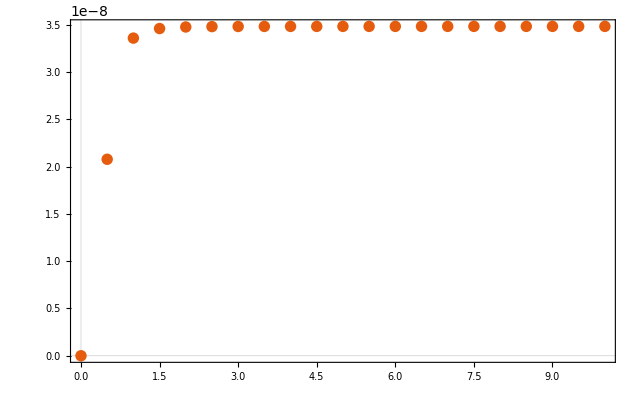

```mathematica
ListPlot[{Extrapolation00}]
```

```mathematica
fitExtrap00=NonlinearModelFit[Extrapolation00[[5;;]], a Log[K] +b + c/K +d/K^2 ,{a,b,c,d},K]
```

FittedModel[3.46159×10^-8-(1.13008×10^-9)/K^2+(7.8946×10^-10)/K+6.69063×10^-11 Log[K]]

```mathematica
fitExtrap00=NonlinearModelFit[Extrapolation00[[5;;]], b + c/K +d/K^2 ,{b,c,d},K]
```

FittedModel[3.48187×10^-8-(6.00294×10^-10)/K^2+(2.16666×10^-10)/K]

```mathematica
fitExtrap00["ParameterConfidenceIntervals"]
```

{{3.48126×10^-8,3.48247×10^-8},{1.64349×10^-10,2.68983×10^-10},{-6.92394×10^-10,-5.08194×10^-10}}

```mathematica
fit1 =First/@fitExtrap00["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
fit2 =Last/@fitExtrap00["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
```

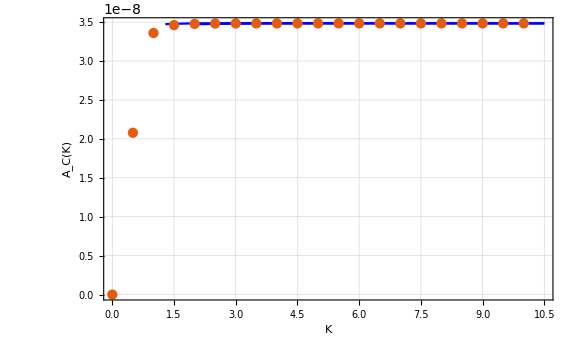

```mathematica
Show[Plot[{fit1,fit2},{k,1,10.5},PlotStyle->Blue,Filling->{1->{2}},GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large],ListPlot[Extrapolation00,PlotRange->All],PlotRange->All]
```

### Intertwiners 11

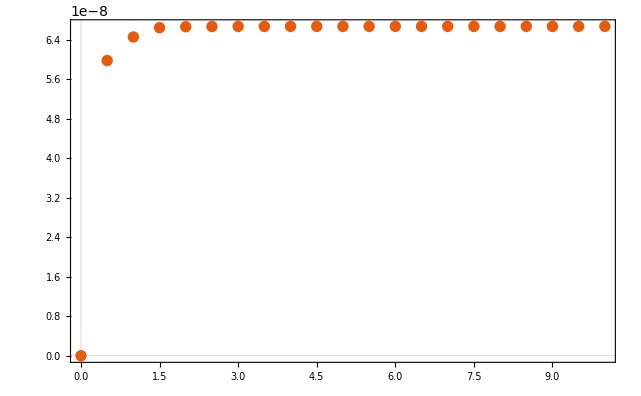

```mathematica
ListPlot[{Extrapolation11}]
```

```mathematica
fitExtrap11=NonlinearModelFit[Extrapolation11[[5;;]], a Log[K] +b + c/K +d/K^2 ,{a,b,c,d},K]
```

FittedModel[6.64959×10^-8-(1.19757×10^-9)/K^2+(8.39159×10^-10)/K+7.14698×10^-11 Log[K]]

```mathematica
fitExtrap11=NonlinearModelFit[Extrapolation11[[5;;]], b + c/K +d/K^2 ,{b,c,d},K]
```

FittedModel[6.67125×10^-8-(6.31654×10^-10)/K^2+(2.27297×10^-10)/K]

```mathematica
fitExtrap11["ParameterConfidenceIntervals"]
```

{{6.6706×10^-8,6.67191×10^-8},{1.7091×10^-10,2.83683×10^-10},{-7.30917×10^-10,-5.3239×10^-10}}

```mathematica
fit1 =First/@fitExtrap11["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
fit2 =Last/@fitExtrap11["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
```

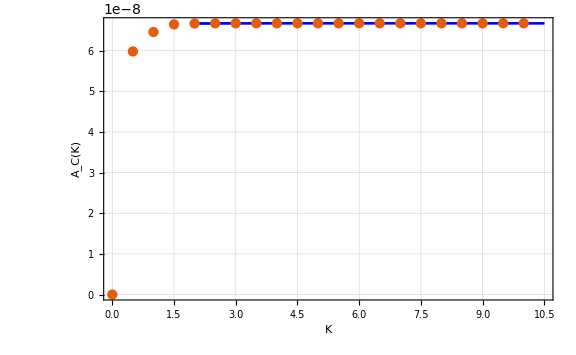

```mathematica
Show[Plot[{fit1,fit2},{k,2,10.5},PlotStyle->Blue,Filling->{1->{2}},GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large],ListPlot[Extrapolation11,PlotRange->All],PlotRange->All]
```

### Intertwiners 01

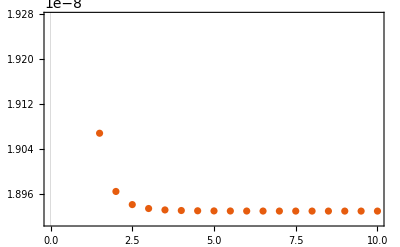

```mathematica
ListPlot[{A01KDl10}]
```

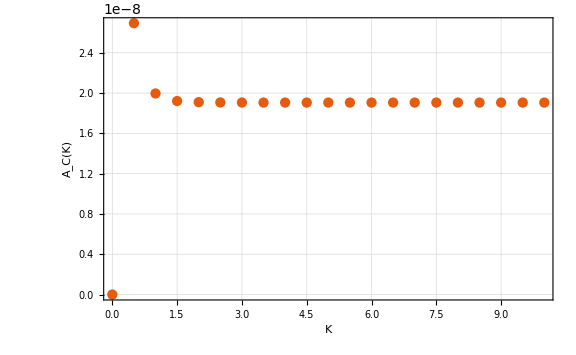

```mathematica
ListPlot[Extrapolation01,PlotRange->All,GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large]
```

# Immirzi 1

## Load the Data

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pdona/Dropbox/Ongoing Projects/OtherEPRLDivergences/Spinfoam_radiative_corrections/Notebooks

```mathematica
DATA = "../data/EPRL/immirzi_1.0/divergence/cutoff_10.0/self_energy_Dl_min_0_Dl_max_10.csv";
```

```mathematica
{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}=Transpose@Import[DATA,"Data",HeaderLines->1];
```

```mathematica
{AKDl0,AKDl1,AKDl2,AKDl3,AKDl4,AKDl5,AKDl6,AKDl7,AKDl8,AKDl9,AKDl10} = Table[{k,#[[2k+1]]},{k,0,10,1/2}]&/@{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10};
```

## Extrapolation using Series convergence acceleration

```mathematica
Aitken[AD_]:=(AD[[-1]]AD[[-3]]-AD[[-2]]^2)/(AD[[-1]]-2AD[[-2]]+AD[[-3]])
```

```mathematica
rExtrapolation= Aitken/@Transpose[{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}]
```

{1.44848×10^-14,2.45288×10^-14,4.44488×10^-14,4.84703×10^-14,4.9605×10^-14,5.00166×10^-14,5.01918×10^-14,5.02754×10^-14,5.03187×10^-14,5.03427×10^-14,5.03568×10^-14,5.03653×10^-14,5.03708×10^-14,5.03744×10^-14,5.03767×10^-14,5.03784×10^-14,5.03795×10^-14,5.03804×10^-14,5.0381×10^-14,5.03814×10^-14,5.03817×10^-14}

```mathematica
Extrapolationg1=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1,10,1/2}]&@rExtrapolation]
```

{{0,0},{1,4.44488×10^-14},{3/2,4.84703×10^-14},{2,4.9605×10^-14},{5/2,5.00166×10^-14},{3,5.01918×10^-14},{7/2,5.02754×10^-14},{4,5.03187×10^-14},{9/2,5.03427×10^-14},{5,5.03568×10^-14},{11/2,5.03653×10^-14},{6,5.03708×10^-14},{13/2,5.03744×10^-14},{7,5.03767×10^-14},{15/2,5.03784×10^-14},{8,5.03795×10^-14},{17/2,5.03804×10^-14},{9,5.0381×10^-14},{19/2,5.03814×10^-14},{10,5.03817×10^-14}}

```mathematica
fitExtrapg1=NonlinearModelFit[Extrapolationg1[[5;;]], a Log[K] +b + c/K +d/K^2 ,{a,b,c,d},K]
```

FittedModel[4.94112×10^-14-(8.05473×10^-15)/K^2+(4.09874×10^-15)/K+2.79236×10^-16 Log[K]]

```mathematica
fitExtrapg1=NonlinearModelFit[Extrapolationg1[[5;;]], b + c/K +d/K^2 ,{b,c,d},K]
```

FittedModel[5.02859×10^-14-(5.12774×10^-15)/K^2+(1.39859×10^-15)/K]

```mathematica
fitExtrapg1["ParameterConfidenceIntervals"]
```

{{5.02643×10^-14,5.03075×10^-14},{1.18913×10^-15,1.60805×10^-15},{-5.56553×10^-15,-4.68995×10^-15}}

```mathematica
fit1 =First/@fitExtrapg1["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
fit2 =Last/@fitExtrapg1["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
```

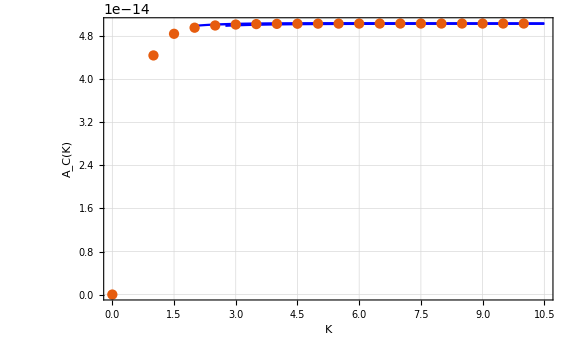

```mathematica
Show[Plot[{fit1,fit2},{k,2,10.5},PlotStyle->Blue,Filling->{1->{2}},GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large],ListPlot[Extrapolationg1,PlotRange->All],PlotRange->All]
```

# Immirzi 0.1 and dimension (2j+1)^2

## Load the Data

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pdona/Dropbox/Ongoing Projects/OtherEPRLDivergences/Spinfoam_radiative_corrections/Notebooks

```mathematica
DATA = "../data/EPRL/immirzi_0.1/divergence/cutoff_10.0/self_energy_Dl_min_0_Dl_max_10_dim_2.csv";
```

```mathematica
{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}=Transpose@Import[DATA,"Data",HeaderLines->1];
```

```mathematica
{AKDl0,AKDl1,AKDl2,AKDl3,AKDl4,AKDl5,AKDl6,AKDl7,AKDl8,AKDl9,AKDl10} = Table[{k,#[[2k+1]]},{k,0,10,1/2}]&/@{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10};
```

## Extrapolation using Series convergence acceleration

```mathematica
Aitken[AD_]:=(AD[[-1]]AD[[-3]]-AD[[-2]]^2)/(AD[[-1]]-2AD[[-2]]+AD[[-3]])
```

```mathematica
rExtrapolation= Aitken/@Transpose[{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}]
```

{1.75327×10^-8,3.05268×10^-8,6.96291×10^-8,7.7824×10^-8,8.03047×10^-8,8.12856×10^-8,8.17454×10^-8,8.19872×10^-8,8.21254×10^-8,8.22094×10^-8,8.22631×10^-8,8.22987×10^-8,8.23231×10^-8,8.23403×10^-8,8.23528×10^-8,8.23619×10^-8,8.23687×10^-8,8.23739×10^-8,8.23779×10^-8,8.23811×10^-8,8.23835×10^-8}

```mathematica
Extrapolation=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1/2,10,1/2}]&@rExtrapolation]
```

{{0,0},{1/2,3.05268×10^-8},{1,6.96291×10^-8},{3/2,7.7824×10^-8},{2,8.03047×10^-8},{5/2,8.12856×10^-8},{3,8.17454×10^-8},{7/2,8.19872×10^-8},{4,8.21254×10^-8},{9/2,8.22094×10^-8},{5,8.22631×10^-8},{11/2,8.22987×10^-8},{6,8.23231×10^-8},{13/2,8.23403×10^-8},{7,8.23528×10^-8},{15/2,8.23619×10^-8},{8,8.23687×10^-8},{17/2,8.23739×10^-8},{9,8.23779×10^-8},{19/2,8.23811×10^-8},{10,8.23835×10^-8}}

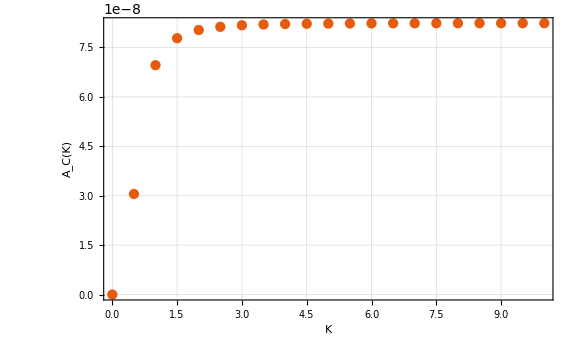

```mathematica
ListPlot[Extrapolation,PlotRange->All,GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large]
```

```mathematica
fitExtrap=NonlinearModelFit[Extrapolation[[5;;]],a k^3+ b k^2 + c k+ d,{a,b,c,d},k]
```

FittedModel[7.70497×10^-8+2.39291×10^-9 k-3.4721×10^-10 k^2+1.62434×10^-11 k^3]

```mathematica
(Normal[fitExtrap]/.Plus->List)/.k->10
```

{7.70497×10^-8,2.39291×10^-8,-3.4721×10^-8,1.62434×10^-8}

```mathematica
fitExtrap["BestFitParameters"]
```

{a→1.62434×10^-11,b→-3.4721×10^-10,c→2.39291×10^-9,d→7.70497×10^-8}

# Immirzi 0.1 and dimension (2j+1)^3

## Load the Data

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pdona/Dropbox/Ongoing Projects/OtherEPRLDivergences/Spinfoam_radiative_corrections/Notebooks

```mathematica
DATA = "../data/EPRL/immirzi_0.1/divergence/cutoff_10.0/self_energy_Dl_min_0_Dl_max_10_dim_3.csv";
```

```mathematica
{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}=Transpose@Import[DATA,"Data",HeaderLines->1];
```

```mathematica
{AKDl0,AKDl1,AKDl2,AKDl3,AKDl4,AKDl5,AKDl6,AKDl7,AKDl8,AKDl9,AKDl10} = Table[{k,#[[2k+1]]},{k,0,10,1/2}]&/@{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10};
```

## Extrapolation using Series convergence acceleration

```mathematica
Aitken[AD_]:=(AD[[-1]]AD[[-3]]-AD[[-2]]^2)/(AD[[-1]]-2AD[[-2]]+AD[[-3]])
```

```mathematica
rExtrapolation= Aitken/@Transpose[{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}]
```

{1.75327×10^-8,6.95165×10^-8,1.9267×10^-7,2.59755×10^-7,2.97563×10^-7,3.21436×10^-7,3.3777×10^-7,3.49588×10^-7,3.58492×10^-7,3.65406×10^-7,3.70904×10^-7,3.75358×10^-7,3.79024×10^-7,3.82081×10^-7,3.84658×10^-7,3.86851×10^-7,3.88733×10^-7,3.90361×10^-7,3.91777×10^-7,3.93017×10^-7,3.94107×10^-7}

```mathematica
Extrapolation=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1/2,10,1/2}]&@rExtrapolation]
```

{{0,0},{1/2,6.95165×10^-8},{1,1.9267×10^-7},{3/2,2.59755×10^-7},{2,2.97563×10^-7},{5/2,3.21436×10^-7},{3,3.3777×10^-7},{7/2,3.49588×10^-7},{4,3.58492×10^-7},{9/2,3.65406×10^-7},{5,3.70904×10^-7},{11/2,3.75358×10^-7},{6,3.79024×10^-7},{13/2,3.82081×10^-7},{7,3.84658×10^-7},{15/2,3.86851×10^-7},{8,3.88733×10^-7},{17/2,3.90361×10^-7},{9,3.91777×10^-7},{19/2,3.93017×10^-7},{10,3.94107×10^-7}}

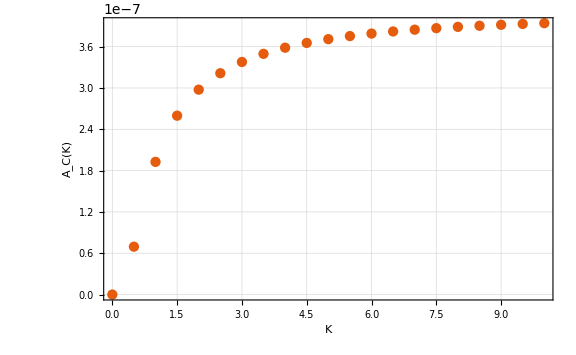

```mathematica
ListPlot[Extrapolation,PlotRange->All,GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large]
```

```mathematica
fitExtrap=NonlinearModelFit[Extrapolation[[5;;]],a k^3+ b k^2 + c k+ d,{a,b,c,d},k]
```

FittedModel[1.93063×10^-7+6.99829×10^-8 k-8.68253×10^-9 k^2+3.71483×10^-10 k^3]

```mathematica
(Normal[fitExtrap]/.Plus->List)/.k->10
```

{1.93063×10^-7,6.99829×10^-7,-8.68253×10^-7,3.71483×10^-7}

```mathematica
fitExtrap["BestFitParameters"]
```

{a→3.71483×10^-10,b→-8.68253×10^-9,c→6.99829×10^-8,d→1.93063×10^-7}

# Immirzi 0.1 and dimension (2j+1)^4

## Load the Data

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pdona/Dropbox/Ongoing Projects/OtherEPRLDivergences/Spinfoam_radiative_corrections/Notebooks

```mathematica
DATA = "../data/EPRL/immirzi_0.1/divergence/cutoff_10.0/self_energy_Dl_min_0_Dl_max_10_dim_4.csv";;
```

```mathematica
{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}=Transpose@Import[DATA,"Data",HeaderLines->1];
```

```mathematica
{AKDl0,AKDl1,AKDl2,AKDl3,AKDl4,AKDl5,AKDl6,AKDl7,AKDl8,AKDl9,AKDl10} = Table[{k,#[[2k+1]]},{k,0,10,1/2}]&/@{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10};
```

## Extrapolation using Series convergence acceleration

```mathematica
Aitken[AD_]:=(AD[[-1]]AD[[-3]]-AD[[-2]]^2)/(AD[[-1]]-2AD[[-2]]+AD[[-3]])
```

```mathematica
rExtrapolation= Aitken/@Transpose[{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}]
```

{1.75327×10^-8,2.2548×10^-7,6.47581×10^-7,1.20849×10^-6,1.78997×10^-6,2.37353×10^-6,2.95516×10^-6,3.53372×10^-6,4.10876×10^-6,4.68012×10^-6,5.24778×10^-6,5.81189×10^-6,6.37273×10^-6,6.93061×10^-6,7.4859×10^-6,8.03896×10^-6,8.59009×10^-6,9.13954×10^-6,9.6875×10^-6,0.0000102341,0.0000107793}

```mathematica
Extrapolation=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1/2,10,1/2}]&@rExtrapolation]
```

{{0,0},{1/2,2.2548×10^-7},{1,6.47581×10^-7},{3/2,1.20849×10^-6},{2,1.78997×10^-6},{5/2,2.37353×10^-6},{3,2.95516×10^-6},{7/2,3.53372×10^-6},{4,4.10876×10^-6},{9/2,4.68012×10^-6},{5,5.24778×10^-6},{11/2,5.81189×10^-6},{6,6.37273×10^-6},{13/2,6.93061×10^-6},{7,7.4859×10^-6},{15/2,8.03896×10^-6},{8,8.59009×10^-6},{17/2,9.13954×10^-6},{9,9.6875×10^-6},{19/2,0.0000102341},{10,0.0000107793}}

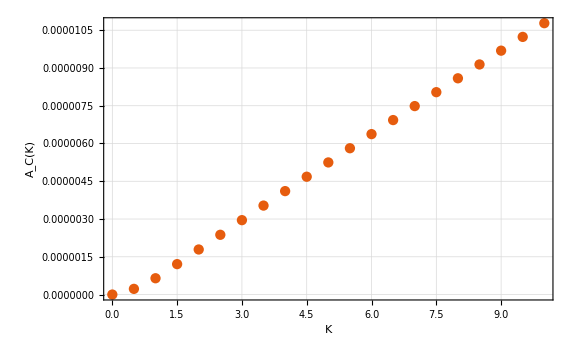

```mathematica
ListPlot[Extrapolation,PlotRange->All,GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large]
```

```mathematica
fitExtrap=NonlinearModelFit[Extrapolation[[5;;]],a k^3+ b k^2 + c k+ d,{a,b,c,d},k]
```

FittedModel[-6.04079×10^-7+1.21621×10^-6 k-1.06145×10^-8 k^2+2.8216×10^-10 k^3]

```mathematica
(Normal[fitExtrap]/.Plus->List)/.k->10
```

{-6.04079×10^-7,0.0000121621,-1.06145×10^-6,2.8216×10^-7}

```mathematica
fitExtrap["BestFitParameters"]
```

{a→2.8216×10^-10,b→-1.06145×10^-8,c→1.21621×10^-6,d→-6.04079×10^-7}

```mathematica
fitExtrap=NonlinearModelFit[Extrapolation[[5;;]],c k+ d,{a,b,c,d},k]
```

FittedModel[-3.95264×10^-7+1.12234×10^-6 k]